```mathematica
n
```

```mathematica
Import["C:\\Users\\douwm\\repos\\ca_compression\\functions_to_find_compression_rules.wl"]
```

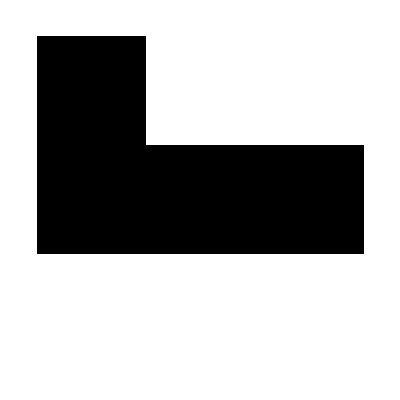
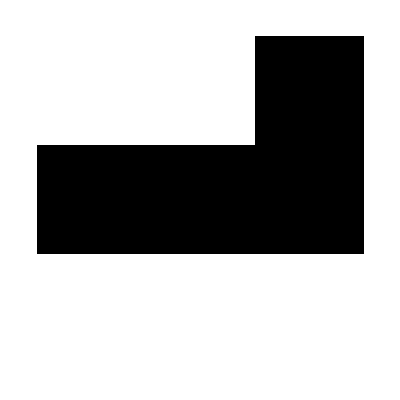
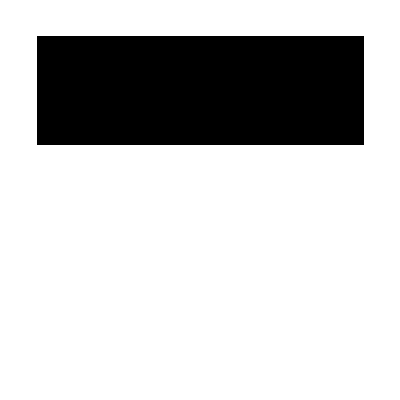
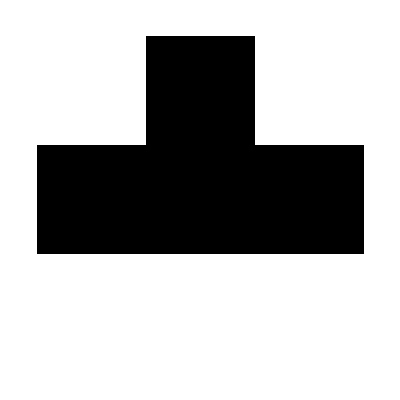
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{4,4,2}

ArrayPlot::mat: Argument {4,4,2} at position 1 is not a list of lists.

ArrayPlot[{4,4,2}]

```mathematica
evols = getEvolutionsForAllPermutations[ruleNumber = 30,ruleRange = 1, dataDimensionality = 3];
ArrayPlot/@evols
updatesPerReadIndex = numberOfUpdatesToDistinguishPermutation[evols,3]
ArrayPlot@updatesPerReadIndex
```

```mathematica
numberOfUpdatesToDistinguishPermutation[evols,3]
```

{4,4,2}

```mathematica
CellularAutomaton[{ruleNumber,2,ruleRange},{1,0,0,0,1,1},5]
```

{{1,0,0,0,1,1},{0,1,0,1,1,0},{1,1,0,1,0,1},{0,0,0,1,0,1},{1,0,1,1,0,1},{0,0,1,0,0,1}}

```mathematica
CellularAutomaton[{ruleNumber,2,ruleRange},{1,0,0,0,1,1},{{1,5},All}]
```

{{0,1,0,1,1,0},{1,1,0,1,0,1},{0,0,0,1,0,1},{1,0,1,1,0,1},{0,0,1,0,0,1}}

```mathematica
noutda =numberOfUpdatesToDistinguishAnyPermutation[evols,dataDimensionality]
```

{{4,4,4},{2,4,4},{4,4,2},{4,4,4},{4,2,4},{4,4,4},{4,4,4},{4,4,4}}

```mathematica
Min[Max/@Transpose[noutda]]
```

4

```mathematica
Last@testRuleRangeDimForReduction[ruleNumber = 30, ruleRange = 1, dataDimensionality = 3]
```

{{4,4,4},{2,4,4},{4,4,2},{4,4,4},{4,2,4},{4,4,4},{4,4,4},{4,4,4}}

```mathematica
a =4<3
```

False

```mathematica
a
```

False

Look at time increase with dimensionality to search for a rule

{0.0002898,0.0001761,0.0003813,0.0010593,0.0034047,0.0201093,0.0908853,2.64158}

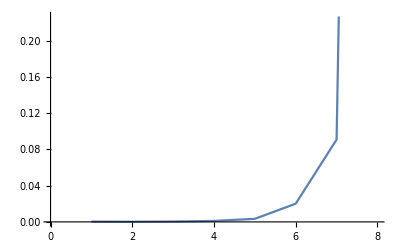

```mathematica
First@AbsoluteTiming@testRuleRangeDimForReduction[ruleNumber = 30, ruleRange = 1, dataDimensionality = #]&/@Range[8]
ListLinePlot@%
```

Look at time increase with rule range increase

{0.091696,0.0598912,0.06253,0.0641598,0.0668481}

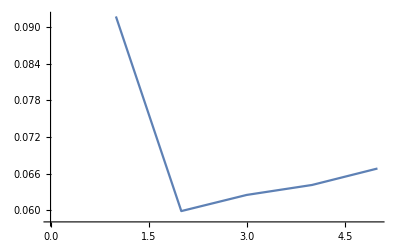

```mathematica
First@AbsoluteTiming@testRuleRangeDimForReduction[ruleNumber = 30, ruleRange = #, dataDimensionality = 7]&/@Range[5]
ListLinePlot@%
```